```mathematica
1/(5*10^-3)//N
```

200.

```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Convert[1/(10Giga Year)*1/(0.3 Giga ElectronVolt/Centimeter^3)1/(10^-3 SpeedOfLight),Barn/(Giga ElectronVolt)]
```

(0.352575 Barn)/(ElectronVolt Giga)

```mathematica
Convert[(1 Centimeter^2)/Gram*ProtonMass/(Giga ElectronVolt),Barn/(Giga ElectronVolt)]//FullSimplify
```

```mathematica
Convert[Barn,Centimeter^2]//N
```

1.×10^-24 Centimeter^2

```mathematica
σHalo=Convert[Barn/(ElectronVolt Giga)mdm Giga ElectronVolt/.mdm->10^logmdm,Centimeter^2] 1/Centimeter^2;
```

```mathematica
σHalo/.logmdm->10//N
```

1.×10^-14

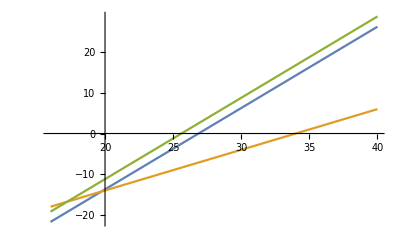

```mathematica
Plot[{Log10[σobsRX],Log10[σCMB],Log10[σCR]},{logmdm,16,40}]
```

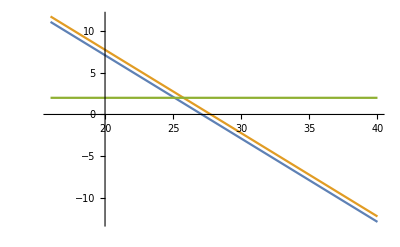

```mathematica
Plot[{Log10[τobsRX],Log10[τCR],Log10[10^2]},{logmdm,16,40}]
```

```mathematica
Convert[3*10^-26 Centimeter^3/Second*1/(10Giga ElectronVolt)*1/(10^-3 SpeedOfLight),Barn/(Giga ElectronVolt)]//N
```

(1.00069×10^-10 Barn)/(ElectronVolt Giga)

```mathematica
σCMB=Convert[(1.0006922855944562*^-10 Barn)/(ElectronVolt Giga)mdm Giga ElectronVolt/.mdm->10^logmdm,Centimeter^2] 1/Centimeter^2;
```